```mathematica
aa="{{   246137.980039070      ,  2.911153846153845E-008 ,  2.911153846153845E-008 ,  0.170621037570220      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      },{  2.911153846153845E-008 ,   246137.980039070      ,  2.911153846153845E-008 ,  0.170621037570220      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      },{  2.911153846153845E-008 ,  2.911153846153845E-008 ,   246137.980039070      ,  0.170621037570220      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      },{  0.170621037570220      ,  0.170621037570220      ,  0.170621037570220      ,   21749.4138462412      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      },{   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   246137.980039070      ,  2.911153846153845E-008 ,  2.911153846153845E-008 ,  7.507325653089685E-002 },{   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,  2.911153846153845E-008 ,   246137.980039070      ,  2.911153846153845E-008 ,  7.507325653089685E-002 },{   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,  2.911153846153845E-008 ,  2.911153846153845E-008 ,   246137.980039070      ,  7.507325653089685E-002 },{   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,   0.00000000000000      ,  7.507325653089685E-002 ,  7.507325653089685E-002 ,  7.507325653089685E-002 ,   155050.586153934      }}";
```

```mathematica
bb=ToExpression[StringReplace[aa,RegularExpression["E([+-][0-9]{3})"]->"*10^($1)"]];
```

```mathematica
Sqrt@Eigenvalues@bb
```

{496.123,496.123,496.123,496.123,496.123,496.123,393.765,147.477}

```mathematica
Sqrt@Eigenvalues@MslepN*10^-9
```

{496.104,496.104,496.104,496.104,496.104,496.104,393.765,147.477}

```mathematica
Sqrt@Eigenvalues@MslepN*10^-9
```

{496.104,496.104,496.104,496.104,496.104,496.104,303.815,290.682}

```mathematica
ML11=ML22=ML33=250GeV;
ML12=ML13=ML23=0;
```

```mathematica
MN33=150GeV;
β=ArcTan[5.0];
```

```mathematica
An11=1000.0GeV;
An12=1000.0GeV;
An13=1000.0GeV;
```

```mathematica
AlambdaN=-250GeV;
```

```mathematica
Yn11=0.000001;
Yn12=0.000001;
Yn13=0.000001;
```

```mathematica
lambda=0.2;
lambdaN=0.05;
kappa=0.1;
phiS=0.0;
phi2=0.0;
```

```mathematica
vevS=130GeV/lambda;
```

```mathematica
Rsc=500GeV;
```

```mathematica
Abtm=1.5TeV;Atop=1.5TeV;Atau=-2.5TeV;
```

```mathematica
MU33=MQ33=MD33=1TeV;
```

```mathematica
Akappa=-200GeV;Alambda=550GeV;ksi=0;
```

```mathematica
MatrixForm@Abs@Sqrt@{{-0.0006376969208941735,-0.0005580109721454525,-0.0006133587594454959,0,0,0},{-0.0005580109721454525,-0.0029758039547908037,0.0005290082375777981,0,0,0},{-0.0006133587594454959,0.0005290082375777981,-0.0001522421276511072,0,0,0},{0,0,0,-0.0006418234248600716,-0.0006382967947964703,-0.0009077447353780147},{0,0,0,-0.0006382967947964703,-0.00034126876801008764,-0.0009077447353780148},{0,0,0,-0.0009077447353780147,-0.0009077447353780148,-0.00001864064131403195}}
```

(0.0252527 | 0.0236223 | 0.0247661 | 0 | 0 | 0
0.0236223 | 0.0545509 | 0.0230002 | 0 | 0 | 0
0.0247661 | 0.0230002 | 0.0123386 | 0 | 0 | 0
0 | 0 | 0 | 0.0253342 | 0.0252645 | 0.0301288
0 | 0 | 0 | 0.0252645 | 0.0184735 | 0.0301288
0 | 0 | 0 | 0.0301288 | 0.0301288 | 0.00431748)

```mathematica
AA={{427325.482921945,-86686.7746880210,-22812.6649130519,0.00000000000000,0.00000000000000,0.00000000000000},{-86686.7746880210,37538.8716685137,3942.00191903358,0.00000000000000,0.00000000000000,0.00000000000000},{-22812.6649130519,3942.00191903358,4960.42710485139,0.00000000000000,0.00000000000000,0.00000000000000},{0.00000000000000,0.00000000000000,0.00000000000000,427010.319635218,85401.7625531915,15763.2215919170},{0.00000000000000,0.00000000000000,0.00000000000000,85401.7625531915,17075.2774352706,3152.64431838340},{0.00000000000000,0.00000000000000,0.00000000000000,15763.2215919170,3152.64431838340,40526.2310688470}};
```

```mathematica
BB={{427325.482921945,-86686.7746880210,-22812.6649130519,0.00000000000000,0.00000000000000,0.00000000000000},{-86686.7746880210,37538.8716685137,3942.00191903358,0.00000000000000,0.00000000000000,0.00000000000000},{-22812.6649130519,3942.00191903358,4960.42710485139,0.00000000000000,0.00000000000000,0.00000000000000},{0.00000000000000,0.00000000000000,0.00000000000000,427010.319635218,85401.7625531915,15763.2215919170},{0.00000000000000,0.00000000000000,0.00000000000000,85401.7625531915,17075.2774352706,3152.64431838340},{0.00000000000000,0.00000000000000,0.00000000000000,15763.2215919170,3152.64431838340,40526.2310688470}};
```

```mathematica
CC={{427325.482921945,-86686.7746880210,-22812.6649130519,0.00000000000000,0.00000000000000,0.00000000000000},{-86686.7746880210,37538.8716685137,3942.00191903358,0.00000000000000,0.00000000000000,0.00000000000000},{-22812.6649130519,3942.00191903358,4960.42710485139,0.00000000000000,0.00000000000000,0.00000000000000},{0.00000000000000,0.00000000000000,0.00000000000000,427010.319635218,85401.7625531915,15763.2215919170},{0.00000000000000,0.00000000000000,0.00000000000000,85401.7625531915,17075.2774352706,3152.64431838340},{0.00000000000000,0.00000000000000,0.00000000000000,15763.2215919170,3152.64431838340,40526.2310688470}};
```

```mathematica
DD={{427325.482921945,-86686.7746880210,-22812.6649130519,0.00000000000000,0.00000000000000,0.00000000000000},{-86686.7746880210,37538.8716685136,3942.00191903358,0.00000000000000,0.00000000000000,0.00000000000000},{-22812.6649130519,3942.00191903358,4960.42710485139,0.00000000000000,0.00000000000000,0.00000000000000},{0.00000000000000,0.00000000000000,0.00000000000000,427010.319635218,85401.7625531915,15763.2215919170},{0.00000000000000,0.00000000000000,0.00000000000000,85401.7625531915,17075.2774352706,3152.64431838340},{0.00000000000000,0.00000000000000,0.00000000000000,15763.2215919170,3152.64431838340,40526.2310688470}};
```

```mathematica
AA-DD
```

{{0.,0.,0.,0.,0.,0.},{0.,9.45874×10^-11,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
MslepN/.{phiS->0,phi2->0,g1->0,g2->0,ML12->0,ML13->0,ML23->0,Yn11->0,Yn12->0,Yn13->0}//MatrixForm
```

(ML11^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ML22^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ML33^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | MN33^2-2 lambda lambdaN v1 v2+2 AlambdaN lambdaN vevS+2 kappa lambdaN vevS^2+4 lambdaN^2 vevS^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ML11^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ML22^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ML33^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | MN33^2+2 lambda lambdaN v1 v2-2 AlambdaN lambdaN vevS-2 kappa lambdaN vevS^2+4 lambdaN^2 vevS^2)

```mathematica
v1v2=v1*v2*10^-18
```

5822.31

```mathematica
Clear[vevS,lambda,kappa]
```

```mathematica
Func[lambda_,kappa_]:=Sqrt@Min[MN33^2-2 lambda lambdaN v1v2+2 AlambdaN lambdaN 200/lambda+2 kappa lambdaN (200/lambda)^2+4 lambdaN^2 (200/lambda)^2,
MN33^2+2 lambda lambdaN v1v2-2 AlambdaN lambdaN 200/lambda-2 kappa lambdaN (200/lambda)^2+4 lambdaN^2 (200/lambda)^2]
```

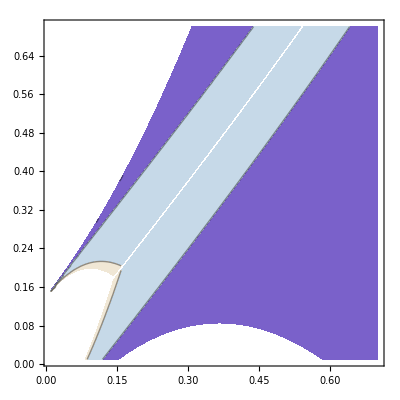

```mathematica
ContourPlot[Func[x,y],{x,0.01,0.7},{y,0.01,0.7},Contours->{0,100,200,500}]
```

```mathematica
M1=200.0;
M2=400.0;
M3=1200.0;
MQ=1000.0;
MQ33=MQ;
MU33=MQ;
MD33=MQ;
M0=250;
Mtau=1.770;
Mtop=173.1;
Mbot=4.6;
MS=0.680474948113042*100.0;
mH1=-0.641092679067157*1000.0;
mH2=-0.295336362674628*1000.0*I;
TANB=5.0;
VEV=174.0;
vevS=650.0;
Yn11=0.000001;
Yn12=0.000001;
Yn13=0.000001;
RT2=Sqrt[2.0];
ALF=1.0/127.9;
MZ=91.188;
SW2=0.2312;
SW=Sqrt[SW2];
CW=Sqrt[1.0-SW2];
TW=SW/CW;
EC=Sqrt[4.0*Pi*ALF];
G=EC/SW;
GP=G*TW;
BETA=ArcTan[TANB];
SINB=Sin[BETA];
COSB=Sqrt[1.0-SINB^2];
lambda=0.2;
lambdaN=0.05;
kappa=0.100;
An11=1000.0;
An12=1000.0;
An13=1000.0;
Alambda=550.0;
AlambdaN=-250.0;
Akappa=-200.0;
Atau=-2500.0;
Atop=1500.0;
Abtm=1500.0;
Rsc=500.0;
phiS=0.0;
phi2=0.0;


g2=G;
v2=VEV*SINB;
v1=VEV*COSB;
g1=G*TW;

Ytop=Mtop/v2;
Ybtm=Mbot/v1;
Ytau=Mtau/v1;
```

```mathematica
Variables@Mne1l
```

{}

```mathematica
Compile
```

```mathematica
Sqrt@Eigenvalues@(Mneut+Mne1l)
```

{668.54,666.881,199.717,138.513,60.821,0.0000127743}

```mathematica
test=Compile[{dummy},Sqrt@Eigenvalues@(Mneut+Mne1l)]
```

Compile::part: Part specification √Eigenvalues[Mneut + Mne1l] ⟦ -1 ⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

CompiledFunction[{dummy},Last[√Eigenvalues[Mneut+Mne1l]],-CompiledCode-]

```mathematica
test[0.948]
```

CompiledFunction::cfse: Compiled expression {{425524.0997277535`, -81093.39036834845`, -21430.002318819643`, 0, 0.`, 0.`}, {-81093.39036834845`, -58369.09377671618`, 4231.401731741455`, 0.`, 0.`, 0.`}, {-21430.002318819643`, 4231.401731741455`, 4958.60924240217`, 0.`, 0.`, 0.`}, {0, 0.`, 0.`, 425202.2647310069`, 79950.`, 14332.167155898489`}, {0.`, 0.`, 0.`, 79950.`, -66414.96869538154`, 2866.433431179701`}, {0.`, 0.`, 0.`, 14332.167155898489`, 2866.433431179701`, 40524.39385778679`}} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

{668.54,666.881,199.717,138.513,60.821,0.0000127743}

```mathematica
LN6[[6,6]]
```

MS^2+lambda^2 v1^2+2 kappa lambda v1 v2+lambda^2 v2^2-2 Akappa kappa vevS+2 kappa^2 vevS^2+1/(64 π^2)3 (-(lambda^2 v2^2 Ybtm^2 (MQ33^2+v1^2 Ybtm^2-DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]))/DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]-(lambda^2 v2^2 Ybtm^2 (-3+2 DLOG[(MQ33^2+v1^2 Ybtm^2-DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2])/Rsc^2]) (MQ33^2+v1^2 Ybtm^2-DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]))/DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]+(lambda^2 v2^2 Ybtm^2 (MQ33^2+v1^2 Ybtm^2+DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]))/DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]+(lambda^2 v2^2 Ybtm^2 (-3+2 DLOG[(MQ33^2+v1^2 Ybtm^2+DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2])/Rsc^2]) (MQ33^2+v1^2 Ybtm^2+DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]))/DSQRT[(Abtm v1-lambda v2 vevS)^2 Ybtm^2]-(lambda^2 v1^2 Ytop^2 (MQ33^2+v2^2 Ytop^2-DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]))/DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]-(lambda^2 v1^2 Ytop^2 (-3+2 DLOG[(MQ33^2+v2^2 Ytop^2-DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2])/Rsc^2]) (MQ33^2+v2^2 Ytop^2-DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]))/DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]+(lambda^2 v1^2 Ytop^2 (MQ33^2+v2^2 Ytop^2+DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]))/DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]+(lambda^2 v1^2 Ytop^2 (-3+2 DLOG[(MQ33^2+v2^2 Ytop^2+DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2])/Rsc^2]) (MQ33^2+v2^2 Ytop^2+DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2]))/DSQRT[(Atop v2-lambda v1 vevS)^2 Ytop^2])

```mathematica
Clear@phiS
```

```mathematica
MS**2+lambda**2*v1**2+2.d0*kappa*lambda*v1*v2+lambda**2*
.v2**2-2.d0*Akappa*kappa*vevS+2.d0*kappa**2*vevS**2+(3.d0*(-
.((lambda**2*v2**2*Ybtm**2*(MD33**2+MQ33**2+2.d0*v1**2*Ybtm**2-
.DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+4.d0*(Abtm*v1-lambda*
.v2*vevS)**2*Ybtm**2)))/DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+
.MQ33**4+4.d0*(Abtm*v1-lambda*v2*vevS)**2*Ybtm**2))-(lambda**2*
.v2**2*Ybtm**2*(-3.d0+2.d0*DLOG((MD33**2+MQ33**2+2.d0*v1**2*
.Ybtm**2-DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+4.d0*(Abtm*v1.-lambda*v2*vevS)**2*Ybtm**2))/(2.d0*Rsc**2)))*(MD33**2+MQ33**2+
.2.d0*v1**2*Ybtm**2-DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+
.4.d0*(Abtm*v1-lambda*v2*vevS)**2*Ybtm**2)))/DSQRT(MD33**4-2.d0*
.MD33**2*MQ33**2+MQ33**4+4.d0*(Abtm*v1-lambda*v2*vevS)**2*
.Ybtm**2)+(lambda**2*v2**2*Ybtm**2*(MD33**2+MQ33**2+2.d0*v1**2*
.Ybtm**2+DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+4.d0*(Abtm*v1.-lambda*v2*vevS)**2*Ybtm**2)))/DSQRT(MD33**4-2.d0*MD33**2*
.MQ33**2+MQ33**4+4.d0*(Abtm*v1-lambda*v2*vevS)**2*Ybtm**2)+
.(lambda**2*v2**2*Ybtm**2*(-3.d0+2.d0*DLOG((MD33**2+MQ33**2+2.d0*
.v1**2*Ybtm**2+DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+4.d0*
.(Abtm*v1-lambda*v2*vevS)**2*Ybtm**2))/(2.d0*Rsc**2)))*(MD33**2+
.MQ33**2+2.d0*v1**2*Ybtm**2+DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+
.MQ33**4+4.d0*(Abtm*v1-lambda*v2*vevS)**2*Ybtm**2)))/
.DSQRT(MD33**4-2.d0*MD33**2*MQ33**2+MQ33**4+4.d0*(Abtm*v1-lambda*
.v2*vevS)**2*Ybtm**2)-(lambda**2*v1**2*Ytop**2*(MQ33**2+MU33**2+
.2.d0*v2**2*Ytop**2-DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-
.lambda*v1*vevS)**2*Ytop**2)))/DSQRT((MQ33**2-MU33**2)**2+4.d0*
.(Atop*v2-lambda*v1*vevS)**2*Ytop**2)-(lambda**2*v1**2*Ytop**2*(-
.3.d0+2.d0*DLOG((MQ33**2+MU33**2+2.d0*v2**2*Ytop**2-
.DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-lambda*v1*vevS)**2*
.Ytop**2))/(2.d0*Rsc**2)))*(MQ33**2+MU33**2+2.d0*v2**2*Ytop**2-
.DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-lambda*v1*vevS)**2*
.Ytop**2)))/DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-lambda*v1*
.vevS)**2*Ytop**2)+(lambda**2*v1**2*Ytop**2*(MQ33**2+MU33**2+2.d0. *v2**2*Ytop**2+DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-lambda*
.v1*vevS)**2*Ytop**2)))/DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-
.lambda*v1*vevS)**2*Ytop**2)+(lambda**2*v1**2*Ytop**2*(-3.d0+2.d0. *DLOG((MQ33**2+MU33**2+2.d0*v2**2*Ytop**2+DSQRT((MQ33**2-
.MU33**2)**2+4.d0*(Atop*v2-lambda*v1*vevS)**2*Ytop**2))/(2.d0*
.Rsc**2)))*(MQ33**2+MU33**2+2.d0*v2**2*Ytop**2+DSQRT((MQ33**2-
.MU33**2)**2+4.d0*(Atop*v2-lambda*v1*vevS)**2*Ytop**2)))/
.DSQRT((MQ33**2-MU33**2)**2+4.d0*(Atop*v2-lambda*v1*vevS)**2*
.Ytop**2)))/(64.d0*Pi**2)
```

```mathematica
Mcχ
```

{{400.,111.227 (DCOS[0.]-ⅈ DSIN[0.])},{22.2453,130. (DCOS[0.]+ⅈ DSIN[0.])}}

```mathematica
Eigenvalues@{{400.,111.22651336322588},{22.2453026726452,130.}}
```

{408.872,121.128}